```mathematica
data=Import["policeshootings2019.json"];
```

```mathematica
allDates="date"/.data;
dates=Select[allDates, StringStartsQ[#,{"2019-01","2019-02","2019-03"}]&];
counts=Counts[dates];
days=31+28+31
```

90

```mathematica
categories=KeySort[Append[Counts[Values[counts]], 0->days-Length[counts]]];
n=Max[Keys[categories]]
For[i=1,i<n,i++,If[KeyExistsQ[categories,i],None,categories[i]=0]];
categories=KeySort[categories]
```

9

<|0→8,1→16,2→22,3→18,4→11,5→7,6→5,7→2,8→0,9→1|>

```mathematica
k=Sum[x*categories[x],{x,Keys[categories]}]/days;
{k,N[k]}
```

{41/15,2.73333}

```mathematica
a=Map[Function[x, (ⅇ^-k k^x)/(x!)],Range[0,n-1]];
a=Append[a,1-Accumulate[a][[-1]]];
{N[a],days*N[a]}
a[[-3]]+=a[[-2]]+a[[-1]];
a=Delete[Delete[a,-1],-1];
expect=days*a;
n=Length[expect];
{N[a],N[expect]}
```

{{0.0650023,0.177673,0.24282,0.221236,0.151178,0.0826438,0.0376488,0.014701,0.00502283,0.00207576},{5.8502,15.9906,21.8538,19.9112,13.606,7.43794,3.38839,1.32309,0.452055,0.186818}}

{{0.0650023,0.177673,0.24282,0.221236,0.151178,0.0826438,0.0376488,0.0217996},{5.8502,15.9906,21.8538,19.9112,13.606,7.43794,3.38839,1.96196}}

```mathematica
observe=Values[categories];
observe[[-3]]+=observe[[-2]]+observe[[-1]];
observe=Delete[Delete[observe,-1],-1]
```

{8,16,22,18,11,7,5,3}

```mathematica
X2=∑_(i=1)^n (expect[[i]]-observe[[i]])^2/expect[[i]];
N[X2]
```

2.81507

```mathematica
P=1-CDF[ChiSquareDistribution[n],X2];
N[P]
```

0.945421

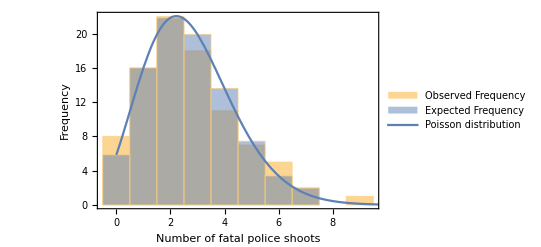

```mathematica
n=Length[observe];
weightedObserveData=WeightedData[Keys[categories],Values[categories]];
weightedExpectData=WeightedData[Range[0,n-1],expect];
fig=Show[
Histogram[
{Legended[weightedObserveData,"Observed Frequency"],
Legended[weightedExpectData,"Expected Frequency"]},n,
Frame->{True,True,False,False},
FrameTicks->{Range[0,n+1],Automatic},
FrameLabel->{"Number of fatal police shoots","Frequency"}
],
Plot[
Legended[Evaluate[days*PDF[PoissonDistribution[k],x]],"Poisson distribution"],{x,0,n+2},
PlotStyle->Thick,
PlotLegends->Automatic
]]
Export["q6.eps",fig];
```